Λ sanity check (expect l(l+1)):

l=1,m=1: 2. (expect 2)

l=3,m=3: 12. (expect 12)

Single test |211⟩ α=0.1, ã=0.99:

Γ·GM (CF)    = 1.15318787696932882438270945649×10^-11

Γ·GM (hydro) = 9.52937×10^-12

Ratio        = 1.21014

Plotting |211⟩ ...

Found 40/40 points  (11 growing, 29 decaying)

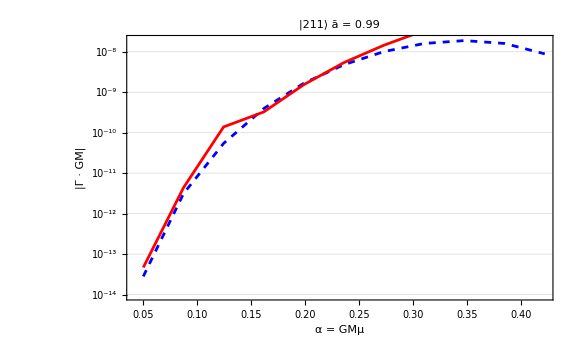

Plotting |433⟩ ...

```mathematica
ClearAll["Global`*"];

prec = 30;

c = 2.99792458*10^(8); (*m/s - Speed of Light*)
G=SetPrecision[1, prec];(*SetPrecision[6.708*10^(-57),100]; (*Newton's gravitational constant*)*)
MSM = 10; (*Input BH mass in solar masses*)
SM = 1.9885*10^(30); (*Solar mass in kg*)
JtoeV = 6.241509*10^18;  (*eV per Joule*)
M =SetPrecision[1, prec]; (* MSM * SM * c^2 * JtoeV; (*BH mass in eV*)*)

(*── Recurrence coefficients (Eqs.25-32,GM=1 units throughout) ──*)
CFCoeffs[n_,ωt_,qt_,at_,m_,l_, α_]:=Module[
{rp,b,Λ,c0,c1,c2,c3,c4,αn, βn, γn},

rp=SetPrecision[1+Sqrt[1-at^2], prec];
b=SetPrecision[Sqrt[1-at^2], prec];


Λ=N[
SpheroidalEigenvalue[
SetPrecision[l, prec],
SetPrecision[m, prec],
I at *G*M*Sqrt[ωt^2-α^2 + 0.I]
], 
prec
];

c0=SetPrecision[1-2I ωt-(2I/b)(ωt-at m/2), prec];

c1=SetPrecision[-4+4I(ωt-I qt(1+b))+(4I/b)(ωt-at m/2)-2(ωt^2+qt^2)/qt, prec];

c2=SetPrecision[3-2I ωt-2(qt^2-ωt^2)/qt-(2I/b)(ωt-at m/2), prec];

c3=SetPrecision[2I(ωt-I qt)^3/qt+2(ωt-I qt)^(2)* b+qt^2 at^2+2I qt at m-Λ-1-(ωt-I qt)^2/qt+2 qt b+(2I/b)((ωt-I qt)^2/qt+1)(ωt-at m/2), prec];

c4=SetPrecision[(ωt-I qt)^4/qt^2+2I ωt(ωt-I qt)^2/qt -(2I/b)(ωt-I qt)^2/qt (ωt-at m/2), prec];

αn = SetPrecision[n^2 + (c0 + 1)*n + c0, prec];
βn = SetPrecision[-2n^2 + (c1 + 2)*n +c3, prec];
γn =SetPrecision[ n^2 + (c2 -3)*n + c4, prec];

{αn, βn, γn}
];

(*── Leaver CF condition f(ω)—zero↔quasi-bound state ──*)
LeaverCF[
ωRe_?NumericQ,ωIm_?NumericQ,at_,m_Integer,l_Integer,α_,Nmax_Integer:400
]:=Module[
{ω,q,R,an,bn,gn,a0,b0,g1},

SetPrecision[μ=α/(G M), prec];

ω=SetPrecision[ωRe+I ωIm, prec];
q=SetPrecision[-Sqrt[μ^2-ω^2+0.I], prec];

R=CFCoeffs[Nmax,ω,q,at,m,l, α][[2]];(*mu at the end?*)

(*Bottom-up sweep*)
Do[
{an,bn,_}=CFCoeffs[n,ω,q,at,m,l, α];
{_,_,gn}=CFCoeffs[n+1,ω,q,at,m,l, α];
R=SetPrecision[bn-an gn/R, prec],
{n,Nmax-1,1,-1}
];
(*f=β₀-α₀ γ₁/R₁*)
{a0,b0,_}=CFCoeffs[0,ω,q,at,m,l, α];
{_,_,g1}=CFCoeffs[1,ω,q,at,m,l, α];

SetPrecision[b0-a0 g1/R, prec]
];

(*── Hydrogen-like growth rate for initial guess (Eq.16) ──*)
HydrogenGamma[n_,l_,m_,α_,at_]:=Module[
{rp,ΩH,ω0,Cnl,glm},

rp=1+Sqrt[1-at^2];
ΩH=at/(2 rp);
ω0=α(1-α^2/(2 n^2));
Cnl=2^(4l+1) (n+l)!/(n^(2l+4)(n-l-1)!)*(l!/((2l)!(2l+1)!))^2;
glm=If[
l==0,1,
Product[k^2(1-at^2)+(at m-2rp α)^2,
{k,1,l}
]
];
2 rp Cnl glm (m ΩH-ω0) α^(4l+5)
];

(*── Root finder ──*)
(*FindQBS[n_,l_,m_,α_?NumericQ,at_?NumericQ,Nmax_:400]:=Module[{ωRe0,ωIm0,ωRe,ωIm,soln,sol,hydro,ratio},ωRe0=α*(1-α^2/(2*n^2));
hydro=HydrogenGamma[n,l,m,α,at];
ωIm0=Max[hydro,10^-6*α^(4*l+6)];
soln=Quiet@FindRoot[{Re@LeaverCF[ωRe,ωIm,at,m,l,α,Nmax],Im@LeaverCF[ωRe,ωIm,at,m,l,α,Nmax]},{{ωRe,ωRe0},{ωIm,ωIm0}},MaxIterations->300,AccuracyGoal->6,PrecisionGoal->6,WorkingPrecision->prec];
If[Head[soln]=!=List,Return[$Failed]];
sol=(ωRe+I*ωIm)/. soln;
If[Im[sol]<=0,Return[$Failed]];
(*Reject if result is more than 4 orders of magnitude above hydrogenic prediction—likely a spurious mode*)If[hydro>0,ratio=Im[sol]/hydro;
If[ratio>10^4||ratio<10^-4,Return[$Failed]]];
(*Reject if real part has drifted far from expected ω~α*)If[Abs[Re[sol]-ωRe0]/α>0.5,Return[$Failed]];
sol]

(* ========================================================PLOT FUNCTION:ΓGM vs α for given state and spin========================================================*)PlotSuperradiance[l_,m_,at_,αMin_:0.05,αMax_:0.5,nPoints_:20,Nmax_:400]:=Module[{n=l+1,αList,cfData,hydroFn},αList=Table[10^x,{x,Log10[αMin],Log10[αMax],(Log10[αMax]-Log10[αMin])/(nPoints-1)}];
(*Compute CF points,skipping failures and negative results*)cfData=Table[Module[{sol},sol=FindQBS[n,l,m,α,at,Nmax];
If[sol=!=$Failed,{α,Im[sol]},Nothing]],{α,αList}];
If[cfData==={},Print["No valid CF points found."];Return[$Failed]];
Print["Found ",Length[cfData]," valid CF points out of ",nPoints];
hydroFn[α_]:=HydrogenGamma[n,l,m,α,at];
Show[(*Analytic hydrogen-like line*)LogLogPlot[hydroFn[α],{α,αMin,αMax},PlotStyle->{Dashed,Blue},PlotRange->All],(*CF numerical points*)ListLogLogPlot[cfData,PlotStyle->{Red,PointSize[0.015]},PlotMarkers->{Automatic,Medium}],Frame->True,FrameLabel->{{"Γ · GM",None},{"α = GMμ",None}},PlotLabel->Style["|"<>ToString[n]<>ToString[l]<>ToString[m]<>"⟩   ã = "<>ToString[at],14,Bold],GridLines->Automatic,GridLinesStyle->Lighter[Gray,0.5],ImageSize->Large,PlotLegends->Placed[{Style["Hydrogen-like",Blue],Style["Leaver CF",Red]},{0.3,0.15}]]]


l =3;
 m=l;
n= l+1;
α=SetPrecision[1.2, prec]; (*Axion-BH Coupling*)
at = 0.99; (*Dimensionless BH Spin*)

(*── Test ──*)

ω211=FindQBS[n,l,m,α,at];
Print["|311>"]
Print["Γ·GM (CF)    = ",Im[ω211] * G M ]
Print["Γ·GM (Non-Rel) = ",HydrogenGamma[n,l,m,α,at] ]
Print["Ratio = ",Im[ω211]/HydrogenGamma[n,l,m,α,at]]

(*Avoid very small α where CF is unreliable;upper limit α<1 for|211⟩*)

PlotSuperradiance[l,m,at,0.05,2,30,300]*)

(*----Single root-finder given an explicit seed----*)(*----Looser drift check that works at large α----*)FindQBSFromSeed[n_,l_,m_,α_?NumericQ,at_?NumericQ,seedRe_?NumericQ,seedIm_?NumericQ,Nmax_:400]:=Module[{ωRe,ωIm,soln,sol},soln=Quiet@FindRoot[{Re@LeaverCF[ωRe,ωIm,at,m,l,α,Nmax],Im@LeaverCF[ωRe,ωIm,at,m,l,α,Nmax]},{{ωRe,seedRe},{ωIm,seedIm}},MaxIterations->300,AccuracyGoal->6,PrecisionGoal->6,WorkingPrecision->prec];
If[Head[soln]=!=List,Return[$Failed]];
sol=(ωRe+I*ωIm)/. soln;
(*Drift check:Re(ω) should stay below α (bound state condition) and not jump by more than half the current step*)If[Re[sol]>1.05*α,Return[$Failed]];(*unbound*)If[Re[sol]<0,Return[$Failed]];(*unphysical*)sol]

PlotSuperradiance[l_,m_,at_,αMin_:0.05,αMax_:1.5,nPoints_:60,Nmax_:400]:=Module[{n=l+1,αList,cfData,prevRe,prevIm,sol,hydro,seedRe,seedIm,hydroData,growingPts,decayingPts,stepSize},(*Denser linear spacing to handle the zero-crossing smoothly*)αList=Table[αMin+(αMax-αMin)*(k-1)/(nPoints-1),{k,1,nPoints}];
cfData={};
prevRe=Null;
prevIm=Null;
Do[hydro=HydrogenGamma[n,l,m,α,at];
Which[(*First point:hydrogenic seed*)prevRe===Null,seedRe=α*(1-α^2/(2*n^2));
seedIm=If[Abs[hydro]>10^-30,hydro,10^-8*α],(*Near the zero crossing:Im is tiny so use a very small seedIm to avoid overshooting to the wrong sheet*)Abs[prevIm]<10^-8*α,seedRe=prevRe;
seedIm=prevIm*0.5,(*shrink toward zero*)(*Normal continuation*)True,seedRe=prevRe;
seedIm=prevIm];
sol=FindQBSFromSeed[n,l,m,α,at,seedRe,seedIm,Nmax];
(*If continuation failed,try a bracket of seedIm values*)If[sol===$Failed,Do[sol=FindQBSFromSeed[n,l,m,α,at,α*(1-α^2/(2*n^2)),trialIm,Nmax];
If[sol=!=$Failed,Break[]],{trialIm,{Abs[hydro],-Abs[hydro],10^-8*α,-10^-8*α,If[prevIm=!=Null,prevIm,10^-8*α],If[prevIm=!=Null,-prevIm,-10^-8*α]}}]];
If[sol=!=$Failed,prevRe=Re[sol];
prevIm=Im[sol];
AppendTo[cfData,{α,Im[sol]}],Print["  No solution at α = ",N[α,4]]],{α,αList}];
If[cfData==={},Print["No valid points."];Return[$Failed]];
growingPts=Cases[cfData,{a_,g_}/;g>0];
decayingPts=Cases[cfData,{a_,g_}/;g<=0:>{a,-g}];
Print["Found ",Length[cfData],"/",nPoints," points  (",Length[growingPts]," growing, ",Length[decayingPts]," decaying)"];
hydroData=Table[Module[{g=HydrogenGamma[n,l,m,α,at]},If[g>0,{α,g},Nothing]],{α,αList}];
Show[ListLogPlot[hydroData,PlotStyle->{Dashed,Blue},Joined->True,PlotRange->All],If[growingPts=!={},ListLogPlot[growingPts,PlotStyle->{Red,PointSize[0.013]},Joined->True],{}],If[decayingPts=!={},ListLogPlot[decayingPts,PlotStyle->{Darker[Green],PointSize[0.013]},Joined->True],{}],Frame->True,FrameLabel->{{"|Γ · GM|",None},{"α = GMμ",None}},PlotLabel->Style["|"<>ToString[n]<>ToString[l]<>ToString[m]<>"⟩   ã = "<>ToString[at],14,Bold],GridLines->{None,Automatic},GridLinesStyle->Lighter[Gray,0.5],ImageSize->Large,PlotLegends->Placed[{Style["Hydrogen-like",Blue],Style["CF  Γ > 0",Red],Style["CF  |Γ|, Γ < 0",Darker[Green]]},{0.25,0.15}]]]

(*----Sanity check----*)
Print["Λ sanity check (expect l(l+1)):"];
Print["  l=1,m=1: ",N[SpheroidalEigenvalue[1,1,0]]," (expect 2)"];
Print["  l=3,m=3: ",N[SpheroidalEigenvalue[3,3,0]]," (expect 12)"];

(*----Single point test----*)
l=1;m=1;n=l+1;at=0.99;
α=SetPrecision[0.1,prec];
hydro0=HydrogenGamma[n,l,m,α,at];
sol0=FindQBSFromSeed[n,l,m,α,at,α*(1-α^2/(2*n^2)),hydro0,400];
Print["\nSingle test |211⟩ α=0.1, ã=0.99:"];
Print["  Γ·GM (CF)    = ",Im[sol0]];
Print["  Γ·GM (hydro) = ",hydro0];
Print["  Ratio        = ",Im[sol0]/hydro0];

(*----Generate plots----*)
Print["\nPlotting |211⟩ ..."];
PlotSuperradiance[1,1,0.99,0.05,1.5,40,300]

Print["\nPlotting |433⟩ ..."];
PlotSuperradiance[3,3,0.99,0.05,1.5,40,300]
```